## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; Q=0.999; r1 = 40; mu = 0.2;
```

```mathematica
winit=(0.25-0.00005*I)
```

0.25-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
qscal = 0.5; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.240421+1.17367×10^-8 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
qscal = 0.5; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ; wc=qscal*Q/rp
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-I*rp^2*(wres-wc)/(rp-rm);
sigmasol=(qscal*Q*wres+M*mu^2-2*M*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  wres-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

0.478123

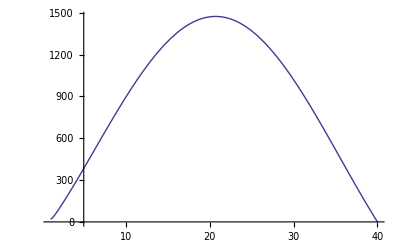

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,rp,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.25+0.000001*I);
ie=0;While[ie<201,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
qscal = 0.5 +ie/200; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
qscals[ie]=qscal/mu;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[qscals[n],10],Re[witer[n]]},{n,0,200}];
t2r=Table[{N[qscals[n],10],Im[witer[n]]},{n,0,200}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.25+0.000001*I);
ie=0;While[ie<101,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
qscal = 0.5 - ie/200; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
qscals[ie]=qscal/mu;
winit=wres+0.001;
ie=ie+1

]
t1l=Table[{N[qscals[n],10],Re[witer[n]]},{n,0,100}];
t2l=Table[{N[qscals[n],10],Im[witer[n]]},{n,0,100}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{2.5,1.17367×10^-8},{2.475,1.11851×10^-8},{2.45,1.06496×10^-8},{2.425,1.01306×10^-8},{2.4,9.62731×10^-9},{2.375,9.13982×10^-9},{2.35,8.66808×10^-9},{2.325,8.21163×10^-9},{2.3,7.77054×10^-9},{2.275,7.34428×10^-9},{2.25,6.93288×10^-9},{2.225,6.53611×10^-9},{2.2,6.15349×10^-9},{2.175,5.78756×10^-9},{2.15,5.43153×10^-9},{2.125,5.09119×10^-9},{2.1,4.76459×10^-9},{2.075,4.45134×10^-9},{2.05,4.15135×10^-9},{2.025,3.86425×10^-9},{2.,3.5898×10^-9},{1.975,3.32828×10^-9},{1.95,3.07899×10^-9},{1.925,2.84178×10^-9},{1.9,2.61642×10^-9},{1.875,2.40286×10^-9},{1.85,2.20178×10^-9},{1.825,2.0097×10^-9},{1.8,1.82964×10^-9},{1.775,1.66033×10^-9},{1.75,1.50142×10^-9},{1.725,1.35278×10^-9},{1.7,1.21404×10^-9},{1.675,1.08454×10^-9},{1.65,9.65251×10^-10},{1.625,8.5449×10^-10},{1.6,7.52806×10^-10},{1.575,6.58593×10^-10},{1.55,5.74218×10^-10},{1.525,4.96468×10^-10},{1.5,4.26968×10^-10},{1.475,3.64189×10^-10},{1.45,3.08131×10^-10},{1.425,2.58399×10^-10},{1.4,1.17093×10^-10},{1.375,1.79151×10^-10},{1.35,1.42592×10^-10},{1.325,1.13391×10^-10},{1.3,8.93271×10^-11},{1.275,6.54875×10^-11},{1.25,4.4284×10^-11},{1.225,2.42666×10^-11},{1.2,5.13485×10^-12},{1.175,-2.05697×10^-11},{1.15,-4.72102×10^-11},{1.125,-8.20159×10^-11},{1.1,-1.2712×10^-10},{1.075,-1.86704×10^-10},{1.05,-2.68062×10^-10},{1.025,-3.67788×10^-10},{1.,-5.01466×10^-10},{0.975,-6.73653×10^-10},{0.95,-8.92786×10^-10},{0.925,-1.16719×10^-9},{0.9,-1.51316×10^-9},{0.875,-1.93853×10^-9},{0.85,-2.4596×10^-9},{0.825,-3.09102×10^-9},{0.8,-3.85313×10^-9},{0.775,-4.76321×10^-9},{0.75,-5.84594×10^-9},{0.725,-7.12546×10^-9},{0.7,-8.62815×10^-9},{0.675,-1.03852×10^-8},{0.65,-1.24298×10^-8},{0.625,-1.47987×10^-8},{0.6,-1.75327×10^-8},{0.575,-2.06763×10^-8},{0.55,-2.42783×10^-8},{0.525,-2.83934×10^-8},{0.5,-3.30661×10^-8},{0.475,-3.84008×10^-8},{0.45,-4.44288×10^-8},{0.425,-5.12401×10^-8},{0.4,-5.89191×10^-8},{0.375,-6.7557×10^-8},{0.35,-7.72546×10^-8},{0.325,-8.81195×10^-8},{0.3,-1.00274×10^-7},{0.275,-1.13842×10^-7},{0.25,-1.28968×10^-7},{0.225,-1.45801×10^-7},{0.2,-1.64506×10^-7},{0.175,-1.85269×10^-7},{0.15,-2.08276×10^-7},{0.125,-2.33743×10^-7},{0.1,-2.61895×10^-7},{0.075,-2.92987×10^-7},{0.05,-3.27277×10^-7},{0.025,-3.65061×10^-7},{0.,-4.06647×10^-7}}

```mathematica
(*The imaginary part vs the radius*)
```

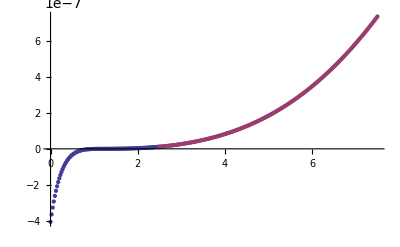

```mathematica
ListPlot[{t2l,t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

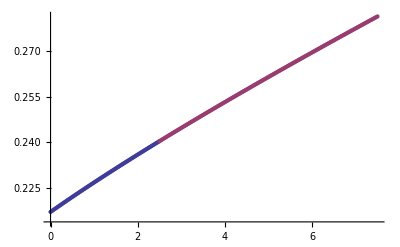

```mathematica
ListPlot[{t1l,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/q/mu0.2/r=40/Q=0.999/R.dat",Join[t1l,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/q/mu0.2/r=40/Q=0.999/I.dat",Join[t2l,t2r]]
```

/home/h/skoli/pt/rnef/mathematica/q/mu0.2/r=40/Q=0.999/R.dat

/home/h/skoli/pt/rnef/mathematica/q/mu0.2/r=40/Q=0.999/I.dat